## EOM Lens System

```mathematica
λ=780;
```

```mathematica
ThinLensMatrix[f_]:={{1,0},{-1/f,1}};(*f [mm]*)
```

```mathematica
PropagationMatrix[z_]:={{1,z},{0,1}};(*transformation over space between lenses, z [mm]*)
```

```mathematica
GaussianWaist[z_,w0_]:=w0 Sqrt[1+((z λ)/(π w0^2))^2];(*[mm]*)
```

```mathematica
WaistAfterLens[z_,f_,w0_,θ_]:=Part[ThinLensMatrix[f].{w0,θ},1,1]
```

```mathematica
Plot[WaistAfterLens[z,10,1,0],{z,0,50}]
```

```mathematica
BeamWaist[z_,w0_]:=Piecewise[{{w0,0<z<10},,{}}](*in mm, for w0 also in mm*)
```

```mathematica
s ={1,10}
```

```mathematica
A=ThinLensMatrix[30].s
```

```mathematica
A[[1]]
```

#### Code Debugging

```mathematica
ThinLensMatrix[10].{1,0}
```

{1,-1/10}

```mathematica
Part[ThinLensMatrix[10].{1,0},1]
```

1

```mathematica
ThinLensMatrix[10].PropagationMatrix[z]
```

{{1,z},{-1/10,1-z/10}}

```mathematica
(ThinLensMatrix[10].PropagationMatrix[z]).s
```

```mathematica
{1+10 z,-1/10+10 (1-z/10)}//FullSimplify
```

{1+10 z,99/10-z}

```mathematica
Part[(ThinLensMatrix[10].PropagationMatrix[z]).s,1]
```

1+10 z

```mathematica
Clear[s]
```

Plot the beam coming out of a thin lens of f=10, for the ingoing beam collimated, assuming ideal ray behavior.

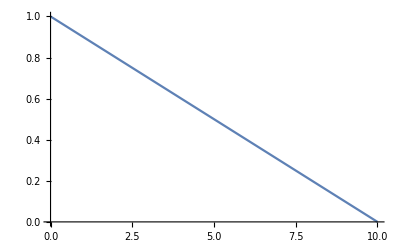

```mathematica
Plot[Part[PropagationMatrix[z].(ThinLensMatrix[10].{1,0}),1],{z,0,10}]
```

How to use Gaussian waist rather than ray trace? Below, GaussianWaist is taking w0 = the width right out of the lens, which is wrong.

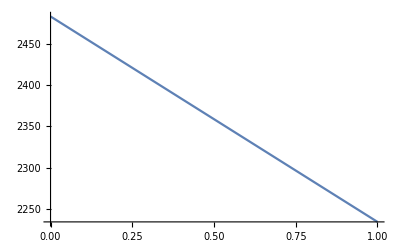

```mathematica
Plot[GaussianWaist[z-10,Part[ThinLensMatrix[10].{1,0},1]],{z,0,1}]
```